```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap1D[];
sizes={128};
timeStep=0.001;
k=0;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{128} | 1 | 128 | {5} | {-5} | {10/127} | {(127 π)/640} | {(127 π)/10}

time | energies | moments | misc
(0) | (total | 0.5
kinetic | 0.25
potential | 0.25
contact | 0.
virial | -9.652×10^-12) | (meanX | 0
sigmaX | 0.707107
norm | 1.) | (steps | 0
A0 | 0.751124)

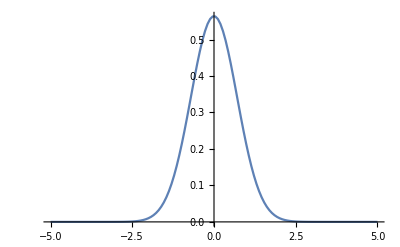

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",30 ,6]]
```

{2.48775,Null}

time | energies | moments | misc
(30.) | (total | 0.5
kinetic | 0.249875
potential | 0.250125
contact | 0.
virial | -0.000500003) | (meanX | 0
sigmaX | 0.707284
norm | 1.) | (steps | 30000
A0 | 0.75103)

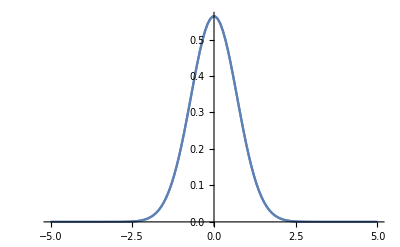

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 0.5 | 0.25 | 0.25 | 0. | -9.652×10^-12
5. | 0.5 | 0.249875 | 0.250125 | 0. | -0.00049998
10. | 0.5 | 0.249875 | 0.250125 | 0. | -0.000500003
15. | 0.5 | 0.249875 | 0.250125 | 0. | -0.000500003
20. | 0.5 | 0.249875 | 0.250125 | 0. | -0.000500003
25. | 0.5 | 0.249875 | 0.250125 | 0. | -0.000500003
30. | 0.5 | 0.249875 | 0.250125 | 0. | -0.000500003

```mathematica
reportMoments
```

time | meanX | sigmaX | norm
0 | 0 | 0.707107 | 1.
5. | 0 | 0.707284 | 1.
10. | 0 | 0.707284 | 1.
15. | 0 | 0.707284 | 1.
20. | 0 | 0.707284 | 1.
25. | 0 | 0.707284 | 1.
30. | 0 | 0.707284 | 1.

```mathematica
reportMisc
```

time | steps | A0
0 | 0 | 0.751124
5. | 5000 | 0.75103
10. | 10000 | 0.75103
15. | 15000 | 0.75103
20. | 20000 | 0.75103
25. | 25000 | 0.75103
30. | 30000 | 0.75103